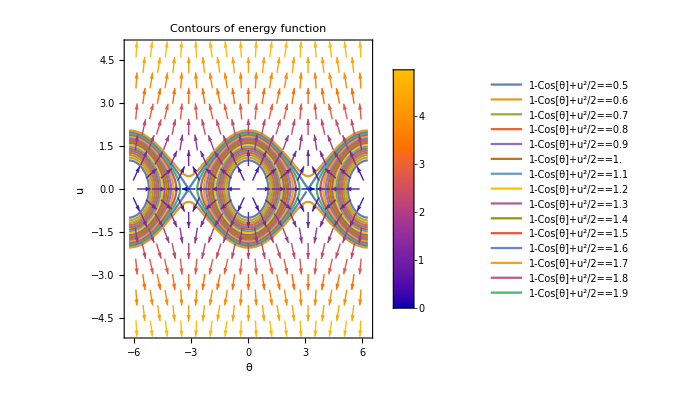

```mathematica
pend={
  θ'[t]==u[t],
  u'[t]==-(g/a)Sin[θ[t]]
} /.{g->1, a->1}; (*Use arbitrary units to get solutions congruent to contours*)
Efun[θ_,u_]:=(1/2)u^2+1-Cos[θ]
{gradFx, gradFy}=Grad[Efun[θ,u], {θ,u}];
cp=ContourPlot[Evaluate@Table[Efun[θ,u]==i, {i,.5,2.1,.1}],{θ,-2π,2π},{u,-5,5}, FrameLabel->{"θ","u"}, PlotLegends->"Expressions"];
vp=VectorPlot[{gradFx,gradFy},{θ,-2π,2π},{u,-5,5}, PlotLegends->Automatic];
Show[cp,vp, PlotLabel->Style["Contours of energy function", FontSize->20]]
```

Note in the above that closed contours exist for very small values of energy of up to 1.6, the point at which it starts making complete revolutions indefinitely (in absence of friction, of course).

Next we solve numerically the system of equations `pend` in the range of t in [-4π,4π] for different IVPs

```mathematica
IVP1={θ[0]==0, u[0]==1.5};
IVP2={θ[0]==0, u[0]==2.5};
sol1 = NDSolve[Join[pend, IVP1],{θ,u},{t,-4π,4π}];
sol2 = NDSolve[Join[pend, IVP2],{θ,u},{t,-4π,4π}];
{Theta1, U1}=First[{θ,u}/.sol1];
{Theta2, U2}=First[{θ,u}/.sol2];
```

```mathematica
energy1 = Efun[Theta1[0],U1[0]];
energy2 = Efun[Theta2[0],U2[0]];
tp1=Plot[Theta1[t],{t,-4π,4π}, PlotStyle-> Pink, PlotLabels->{StringForm[" (θ(0), u(0)) =(0, 1.5), E=``.",energy1]}];
tp2=Plot[Theta2[t],{t,-4π,4π}, PlotLabels->{StringForm[" (θ(0), u(0)) =(0, 2.5), E=``.",energy2]}];
Show[tp1,tp2, PlotRange->{{-4π,4π},{-100,100}},PlotLegends->Automatic, AxesLabel->{t,θ}]
```

-Graphics-

Next we are supposed to find out what range of E does it conserve closed contours. Above we saw that for values <1.6 it conserved closed contours. Does there exist a definite answer? How do we find this? The ideal pendulum will have max potential energy at height h=2a, so if a=1, we have max E=P_maxheight=mhg=hg=2g. For standard units (g=1) we have E=2 is the maximum). For general units and a string length of l, we have E_maxClosedContours=2lmg.

Following we have to modify the above contour plot to colour closed contours blue and open contours red. The contour dividing the closed and open contours should be thick black.

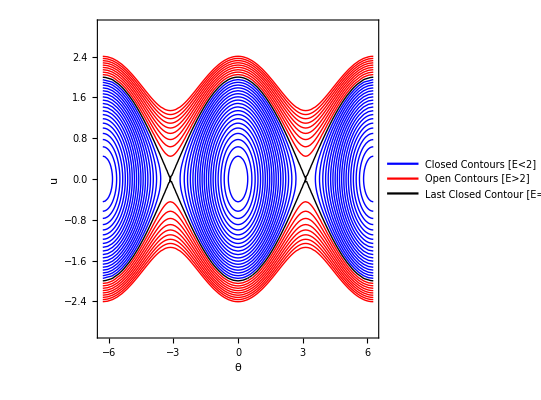

```mathematica
contoursClosed=Table[i,{i,0.1,1.9,.1}];
contourClosed = {2};
contoursOpen =Table[i,{i,2.1,2.9,.1}];
cpClosed=ContourPlot[Efun[θ,u],{θ,-2π,2π},{u,-3,3}, 
                                           FrameLabel->{"θ","u"}, PlotLegends->{"Closed Contours [E<2]"},
                                           Contours->contoursClosed, ContourShading->None, ContourStyle->Blue];
cpOpen=ContourPlot[Efun[θ,u],{θ,-2π,2π},{u,-3,3}, 
                                           FrameLabel->{"θ","u"}, PlotLegends->{"Open Contours [E>2]"},
                                           Contours->contoursOpen, ContourShading->None, ContourStyle->Red];
cpLastClosed=ContourPlot[Efun[θ,u],{θ,-2π,2π},{u,-3,3},
                                           Contours->contourClosed, PlotLegends->{"Last Closed Contour [E=2]"},ContourShading->None, ContourStyle->Thick];
cpOrbits={cpClosed,cpOpen,cpLastClosed};
Show[cpOrbits, PlotLegends->None]
```

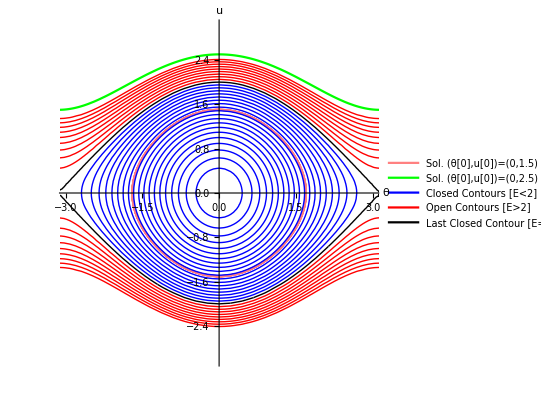

```mathematica
solTrajectory1=ParametricPlot[{Theta1[t],U1[t]}, {t,-4π,4π},
			PlotLegends->{"Sol. (θ[0],u[0])=(0,1.5)"}, PlotStyle->Pink];
solTrajectory2=ParametricPlot[{Theta2[t],U2[t]}, {t,-4π,4π},
			PlotLegends->{"Sol. (θ[0],u[0])=(0,2.5)"}, PlotStyle->Green];
Show[Join[{solTrajectory1,solTrajectory2 },cpOrbits], PlotRange->{{-3,3},{-3,3}},
               PlotLegends->Automatic, AxesLabel->{θ,u}]
```

```mathematica
Manipulate[
IVPAnim={θ[0]==0, u[0]==k};
energyAnim = (1/2)k^2;
solAnim = NDSolve[Join[pend, IVPAnim],{θ,u},{t,0,4π}];
{sol, notSol}=First[{θ,u}/.solAnim];

Animate[Show[{
  Graphics[Line[{{0,0},{l*Sin[sol[t]],-l*Cos[sol[t]]}}]],
    ParametricPlot[{l*Sin[sol[s]],-l*Cos[sol[s]]},{s,0.,t}]
},
PlotRange->{{-l,l},{-1.1 l,2.5}}, PlotLabel->StringForm["Vel ``,Energy ``",k,energyAnim]],
{t,10^-10,15}],{k,0.1,5}]
```